## 运动方程

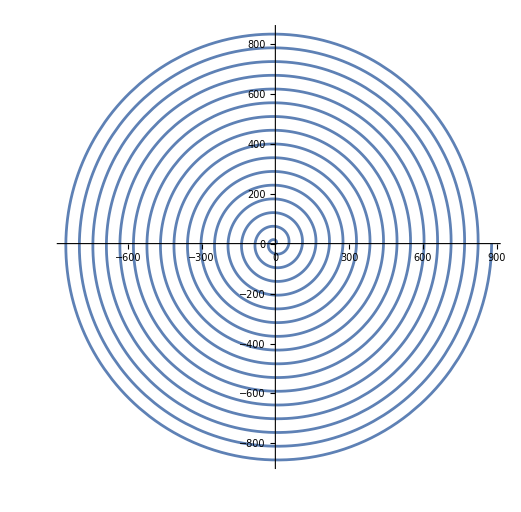

```mathematica
PolarPlot[55/(2 Pi)t,{t,0,16 2 Pi}]
```

```mathematica
DSolve[{55/2/Pi θ[t] D[θ[t],t]==100,θ[0]==32Pi},θ[t],t]
```

DSolve::bvnul: 对于通解的某些分支，给定的边界条件产生一个空解.

{{θ[t]→4 √(π/11) √(704 π+5 t)}}

```mathematica
θ[t_]:=4 √(π/11) √(704 π-5 t)
r[t_]:=55/(2π) 4 √(π/11) √(704 π-5 t)
```

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[
Show[
%1,
Graphics[Point[{r[t]Cos[θ[t]],r[t] Sin[θ[t]]}]]
],{t,0,704Pi/5-0.0001}
]
```

```mathematica
ri[th_]:=55/2/Pi th;
cord[th_]:={ri[th] Cos[th],ri[th] Sin[th]};
```

```mathematica
Clear[th]
```

```mathematica
(*题目条件参数化*)
d1=341-2 27.5
d2=220-2 27.5
thhead=32Pi;
```

286.

165.

```mathematica
eqn[dis_,th_,th0_]:=ri[th0]^2+ri[th]^2-2ri[th0]ri[th]Cos@(-th0+th)==dis^2
```

```mathematica
NSolve[eqn[#,th,th0],th,Reals]&/@{d1,d2}//TableForm
```

NSolve::ratnz: NSolve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

th→ConditionalExpression[th0^2/(-1.+2. th0)-0.0000391297 √((6.97195×10^11-1.39439×10^12 th0-6.53113×10^8 th0^2+1.30623×10^9 th0^3+6.53113×10^8 th0^4)/(-1.+2. th0)^2), th0>12.0885||th0<0.500029] | th→ConditionalExpression[th0^2/(-1.+2. th0)+0.0000391297 √((6.97195×10^11-1.39439×10^12 th0-6.53113×10^8 th0^2+1.30623×10^9 th0^3+6.53113×10^8 th0^4)/(-1.+2. th0)^2), th0>12.0885||th0<0.500029]
th→ConditionalExpression[th0^2/(-1.+2. th0)-0.0000821907 √((5.25965×10^10-1.05193×10^11 th0-1.48032×10^8 th0^2+2.96063×10^8 th0^3+1.48032×10^8 th0^4)/(-1.+2. th0)^2), th0>8.15433||th0<0.500088] | th→ConditionalExpression[th0^2/(-1.+2. th0)+0.0000821907 √((5.25965×10^10-1.05193×10^11 th0-1.48032×10^8 th0^2+2.96063×10^8 th0^3+1.48032×10^8 th0^4)/(-1.+2. th0)^2), th0>8.15433||th0<0.500088]

```mathematica
root=NSolve[eqn[d1,th,thhead],th,Reals]//Timing
```

{0.03125,{{th→-128.947},{th→-128.659},{th→-122.738},{th→-122.302},{th→-116.503},{th→-115.971},{th→-110.253},{th→-109.656},{th→-103.992},{th→-103.352},{th→-97.7193},{th→-97.059},{th→-91.435},{th→-90.7783},{th→-85.1358},{th→-84.5128},{th→-78.8149},{th→-78.2694},{th→-72.4527},{th→-72.0679},{th→69.0117},{th→69.2273},{th→75.1608},{th→75.6415},{th→81.3876},{th→81.9788},{th→87.6434},{th→88.2875},{th→93.917},{th→94.5788},{th→100.204},{th→100.857},{th→106.502},{th→107.124},{th→112.812},{th→113.38},{th→119.134},{th→119.623},{th→125.476},{th→125.848},{th→131.867},{th→132.022}}}

```mathematica
Min@Select[Last/@Flatten@root,#>thhead&]
```

100.857

```mathematica
NestList[-0.0065253582817119725 (27071.751709740965-153.24829025903588 #)&,633.2791709257858,10]
```

{633.279,456.626,279.973,103.321,-73.3323,-249.985,-426.638,-603.291,-779.944,-956.597,-1133.25}

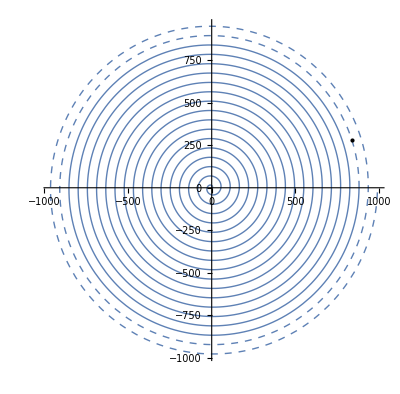

```mathematica
Show[PolarPlot[55/(2 Pi)t,{t,0,16 2 Pi},PlotStyle->Thin],
PolarPlot[55/(2 Pi)t,{t,16 2 Pi,18 2Pi},PlotStyle->{Dashed,Thin}],
Graphics@Point@cord[100.857]
]
```

## 长度约束（龙身）

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[{k0,θ0}]
d1=341-2 27.5
d2=220-2 27.5
thhead=32Pi;
```

286.

165.

```mathematica
ri[th_]:=55/2/Pi th;
x[θ_]:=ri[θ]Cos[θ];
y[θ_]:=ri[θ]Sin[θ];
```

```mathematica
(*切线斜率-长度*)
k[θ_]:=y'[θ]/x'[θ];
ro[θ_]:=Solve[√(1+k0^2)(xx-x[θ])==d2,xx]
```

```mathematica
xc=xx/.First@ro[θ0]
```

(165.+8.75352 √(1.+k0^2) θ0 Cos[θ0])/(√(1.+k0^2))

```mathematica
b[θ_]:=jj/.Solve[k0 x[θ]+jj==y[θ],jj][[1]]
b0=b[θ0]
```

-(55 (k0 θ0 Cos[θ0]-θ0 Sin[θ0]))/(2 π)

```mathematica
yc=k0 xc+b0
```

(k0 (165.+8.75352 √(1.+k0^2) θ0 Cos[θ0]))/(√(1.+k0^2))-(55 (k0 θ0 Cos[θ0]-θ0 Sin[θ0]))/(2 π)

```mathematica
k0=k[θ0]
xc
yc
```

((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π))/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))

(165.+8.75352 θ0 Cos[θ0] √(1.+((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π))^2/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))^2))/(√(1.+((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π))^2/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))^2))

-(55 (-θ0 Sin[θ0]+(θ0 Cos[θ0] ((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π)))/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))))/(2 π)+(((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π)) (165.+8.75352 θ0 Cos[θ0] √(1.+((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π))^2/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))^2)))/(((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π)) √(1.+((55 θ0 Cos[θ0])/(2 π)+(55 Sin[θ0])/(2 π))^2/((55 Cos[θ0])/(2 π)-(55 θ0 Sin[θ0])/(2 π))^2))

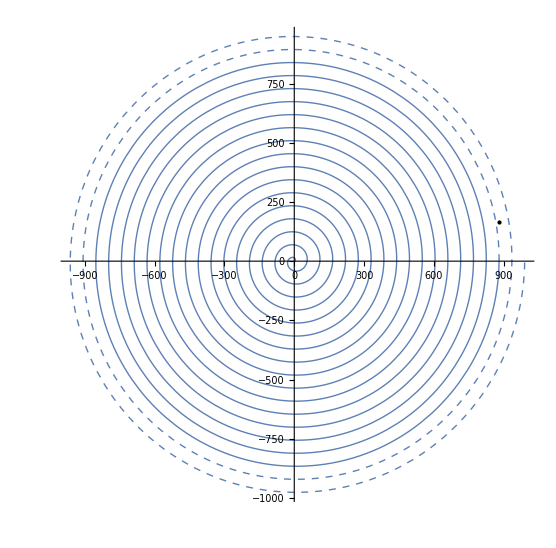

```mathematica
Show[PolarPlot[55/(2 Pi)t,{t,0,16 2 Pi},PlotStyle->Thin],
PolarPlot[55/(2 Pi)t,{t,16 2 Pi,18 2Pi},PlotStyle->{Dashed,Thin}],
Graphics@Point[{xc,yc}]
]
```

```mathematica
{"k_0=",k[Subscript[θ, 0]],"x=",xc,"y=",yc}//TableForm//TraditionalForm
```

k_0=
((55 sin(θ0))/(2 π)+(55 θ0 cos(θ0))/(2 π))/((55 cos(θ0))/(2 π)-(55 θ0 sin(θ0))/(2 π))
x=
(8.75352 θ0 √(k0^2+1.) cos(θ0)+165.)/(√(k0^2+1.))
y=
(k0 (8.75352 θ0 √(k0^2+1.) cos(θ0)+165.))/(√(k0^2+1.))-(55 (θ0 k0 cos(θ0)-θ0 sin(θ0)))/(2 π)

```mathematica
Subscript[θ, 0]=θ0
```

θ0

## 长度约束（龙头）

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[{k0,θ0}]
d1=341-2 27.5;
d2=220-2 27.5;
thhead=32Pi;
ri[th_]:=55/2/Pi th;
x[θ_]:=ri[θ]Cos[θ];
y[θ_]:=ri[θ]Sin[θ];
(*切线斜率-长度*)
k[θ_]:=y'[θ]/x'[θ];
ro[θ_]:=Solve[√(1+k0^2)(xx-x[θ])==d1,xx]
b[θ_]:=jj/.Solve[k0 x[θ]+jj==y[θ],jj][[1]]
```

```mathematica
xc=xx/.First@ro[θ0]
b0=b[θ0]
yc=k0 xc+b0
```

(286.+8.75352 √(1.+k0^2) θ0 Cos[θ0])/(√(1.+k0^2))

-(55 (k0 θ0 Cos[θ0]-θ0 Sin[θ0]))/(2 π)

(k0 (286.+8.75352 √(1.+k0^2) θ0 Cos[θ0]))/(√(1.+k0^2))-(55 (k0 θ0 Cos[θ0]-θ0 Sin[θ0]))/(2 π)

```mathematica
k0=k[32Pi]
θ0=32Pi;
xc
yc
```

32 π

882.845

285.986

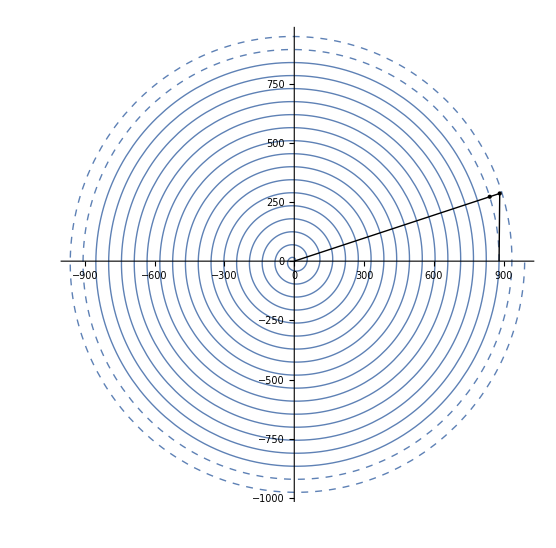

```mathematica
Show[PolarPlot[55/(2 Pi)t,{t,0,16 2 Pi},PlotStyle->Thin],
PolarPlot[55/(2 Pi)t,{t,16 2 Pi,18 2Pi},PlotStyle->{Dashed,Thin}],
Graphics@Point[{{xc,yc},{839.7800024374903,272.0355965061064}}],
Graphics[Line[{{880,0},{882.8447538720744,yc},{0,0}}]]
]
```

```mathematica
{"k_0=",k[Subscript[θ, 0]],"x=",xc,"y=",yc}//TableForm//TraditionalForm
```

k_0=
((55 sin(θ0))/(2 π)+(55 θ0 cos(θ0))/(2 π))/((55 cos(θ0))/(2 π)-(55 θ0 sin(θ0))/(2 π))
x=
(8.75352 θ0 √(k0^2+1.) cos(θ0)+286.)/(√(k0^2+1.))
y=
(k0 (8.75352 θ0 √(k0^2+1.) cos(θ0)+286.))/(√(k0^2+1.))-(55 (θ0 k0 cos(θ0)-θ0 sin(θ0)))/(2 π)

```mathematica
Subscript[θ, 0]=θ0
```

θ0

```mathematica
GiveNextPoint[θ0_]:=Module[{k0=k@θ0},N@ArcTan[yc/xc]]
```

```mathematica
GiveNextPoint[32Pi]
```

ArcTan[(√(1.+k0^2) ((k0 (286.+8.75352 √(1.+k0^2) θ0 Cos[θ0]))/(√(1.+k0^2))-8.75352 (k0 θ0 Cos[θ0]-1. θ0 Sin[θ0])))/(286.+8.75352 √(1.+k0^2) θ0 Cos[θ0])]

```mathematica
xe[θ_]:=(286.+8.753521870054245 √(1.+k0^2) θ0 Cos[θ0])/(√(1.+k0^2));
ye[θ_]:=(k0 (286.+8.753521870054245 √(1.+k0^2) θ0 Cos[θ0]))/(√(1.+k0^2))-(55 (k0 θ0 Cos[θ0]-θ0 Sin[θ0]))/(2 π);
```

```mathematica
GiveNextPoint[θ0_]:=Module[{deg=ArcTan[ye[θ0]/xe[θ0]]+θ0~Mod~2Pi},{ri[deg]Cos[deg],ri[deg]Sin[deg]}]
```

```mathematica
GiveNextPoint[32Pi]
```

{-6.92211,15.9025}

## 龙头运动方程（参数化）

```mathematica
NIntegrate[√(re[t]^2+re'[t]^2),{t,900Pi/170,32Pi}]
```

133004.

```mathematica
DSolve[{d/(2Pi)θ'[t] √(1+θ[t]^2)==v,θ[0]==a},θ[t],t]
```

{{θ[t]→InverseFunction[-1/2 Log[-#1+√(1+#1^2)]+1/2 #1 √(1+#1^2)&][(2 π t v)/d+1/2 (a √(1+a^2)-Log[-a+√(1+a^2)])]}}

```mathematica
-1/2 Log[-#1+√(1+#1^2)]+1/2 #1 √(1+#1^2)&[θ]==(2 π t v)/d+1/2 (a √(1+a^2)-Log[-a+√(1+a^2)])//TraditionalForm
```

1/2 θ √(θ^2+1)-1/2 log(√(θ^2+1)-θ)==1/2 (a √(a^2+1)-log(√(a^2+1)-a))+(2 π t v)/d

```mathematica
With[{θ=InverseFunction[-1/2 Log[-#1+√(1+#1^2)]+1/2 #1 √(1+#1^2)&][(2 π t v)/d+1/2 (a √(1+a^2)-Log[-a+√(1+a^2)])]},-1/2 Log[-#1+√(1+#1^2)]+1/2 #1 √(1+#1^2)&[θ]==(2 π t v)/d+1/2 (a √(1+a^2)-Log[-a+√(1+a^2)])]
```

InverseFunction::ifun: 反函数正在使用中. 对于多值反函数，有些值可能丢失.

True

## 盘入盘出画图

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[#,{t,0,-500},ControlPlacement->Top]&@Show[
(*底盘*)
Graphics[{Yellow,Disk[{0,0},450]}],
ContourPlot[x^2+y^2==450^2,{x,-450,450},{y,-450,450},ContourStyle->{Black,Dashed}],
(*盘入盘出轨迹*)
PolarPlot[170/(2Pi)t,{t,900Pi/170,32Pi},PlotStyle->{Medium}],
PolarPlot[-170/(2Pi)t,{t,900Pi/170,32Pi},PlotStyle->{Dashed,Medium}],
Graphics[Line[{{x1,y1},-{x1,y1}}]],
Graphics[{Circle[]}],
Graphics[{Red,{lines1[[2]],lines2[[2]]}}],
Graphics[{Circle[{x1,y1}-t lines1[[2,2]],Norm[t lines[[2,2]]]],Point[{x1,y1}-t lines1[[2,2]]]}],
Graphics[{Circle[-{x1,y1}+t /2lines1[[2,2]],1/2Norm[t lines[[2,2]]]],Point[-{x1,y1}+t /2lines1[[2,2]]]}],
PlotRange->{{-500,500},{-500,500}}
]
```

```mathematica
ri[th_]:=170/2/Pi th;
x[θ_]:=ri[θ]Cos[θ];
y[θ_]:=ri[θ]Sin[θ];
(*切线斜率-长度*)
k[θ_]:=y'[θ]/x'[θ];
```

```mathematica
k[900Pi/170]//N
```

-0.854069

```mathematica
x1=x[900Pi/170]//N
y1=y[900Pi/170]//N
```

-271.186

-359.108

```mathematica
lines1=InfiniteLine[{x1,y1},#]&/@(Last@FrenetSerretSystem[{x[t],y[t]},t]/.t->900Pi/170);
lines2=InfiniteLine[-{x1,y1},#]&/@(Last@FrenetSerretSystem[{x[t],y[t]},t]/.t->900Pi/170);
```

```mathematica
Expand[r^2+(r+dr)^2-2r(r+dr)Cos[dt]]
```

dr^2+2 dr r+2 r^2-2 dr r Cos[dt]-2 r^2 Cos[dt]

```mathematica
r[t_]:=d/2/Pi θ[t];
DSolve[{1==(d/2/Pi θ'[t])^2+(d/2/Pi θ[t])^2(θ'[t])^2,θ[0]==32Pi},θ[t],t]
```

DSolve::bvnul: 对于通解的某些分支，给定的边界条件产生一个空解.

{}

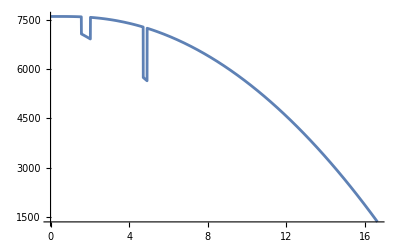

```mathematica
Plot[N[3r1[s](Pi-2dth[s])+2NIntegrate[√(re[t]^2+re'[t]^2),{t,s,900Pi/170}]],{s,0.00001,900Pi/170}]
```

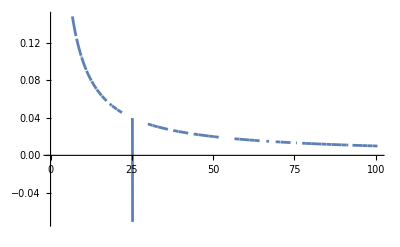

```mathematica
Plot[dth[t],{t,0,32Pi}]
```

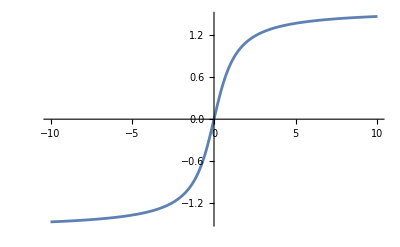

```mathematica
Plot[ArcTan@x,{x,-10,10}]
```

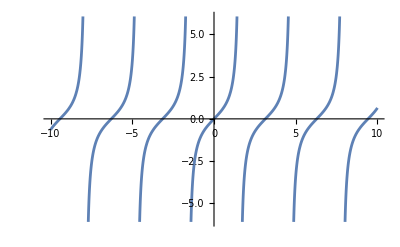

```mathematica
Plot[Tan[x],{x,-10,10}]
```

## 盘入盘出2

```mathematica
(*计算掉头路径时用到的一些函数*)
Clear["Global`*"]
re[th_]:=170/2/Pi th;
Toxy[th_]:={re[th]Cos[th],re[th]Sin[th]};
x[th_]:=Toxy[th][[1]];
y[th_]:=Toxy[th][[2]];
k[th_]:=-x'[th]/y'[th]
cirmid1[th_]:=Toxy[th]-2r1[th] Sign[{1,k[th]}~Dot~Toxy[th]] Normalize[{1,k[th]}];
cirmid2[s_]:=-(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}]);
dth[th_]:=ArcTan[y[th]/x[th]]-ArcTan[k[th]];
r1[th_]:=re[th]/3/Abs@Cos[dth[th]];
dth1[th_]:=ArcCos[(170/Pi th 2/3/2)/(2 r1[th])];
lineq[th_,x1_,y1_]:=x[th]y1==y[th]x1;
endp[leq_,ceq_,x_,y_]:=Last/@#&/@Solve[leq&&ceq,{x,y}]
```

```mathematica
tanth[r_]:=(1+((Sin[(2*Pi*r)/1.7]+(2*Pi*r)/1.7*Cos[(2*Pi*r)/1.7])/(Cos[(2*Pi*r)/1.7]-(2*Pi*r)/1.7*Sin[(2*Pi*r)/1.7]))*Tan[(2*Pi*r)/1.7])/(((Sin[(2*Pi*r)/1.7]+(2*Pi*r)/1.7*Cos[(2*Pi*r)/1.7])/(Cos[(2*Pi*r)/1.7]-(2*Pi*r)/1.7*Sin[(2*Pi*r)/1.7]))-Tan[(2*Pi*r)/1.7]);
```

```mathematica
Manipulate[
Column[{
Show[
(*底盘*)
Graphics[{{Yellow,Disk[{0,0},450]},Point[{0,0}]}],
ContourPlot[x^2+y^2==450^2,{x,-450,450},{y,-450,450},ContourStyle->{Black,Dashed}],
(*盘入盘出轨迹*)
PolarPlot[170/(2Pi)t,{t,s,32Pi},PlotStyle->{Medium}],
PolarPlot[-170/(2Pi)t,{t,s,32Pi},PlotStyle->{Dashed,Medium}],
(*掉头轨迹*)
Graphics[Circle[{0,0},170/(2Pi)s]],
Graphics[Line[{{x[s],y[s]},-{x[s],y[s]}}]],
Graphics[{
Circle[
Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}],
2r1[s],
{ArcTan@@(Toxy[s]-(Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}])),
ArcTan@@(-1/3Toxy[s]-(Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}]))-2Pi}//N
(*{2dth[s]+ArcTan[k[s]],Pi+dth[s]+ArcTan[k[s]]}*)],
{Red,Line[{
Toxy[s],
Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}],
-(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}]),
-Toxy[s]
}]},
Point[{
Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}],
-(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}])
}]
}],

Graphics[Circle[
-(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}]),re[s]/Abs@Cos[dth[s]]/3,
{ArcTan@@(-Toxy[s]+(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}])),
ArcTan@@(-1/3Toxy[s]+(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}]))}//N
(*{Pi+dth[s]+ArcTan[k[s]],2Pi-2dth[s]+ArcTan[k[s]]}]],
{3Pi/2-dth[s]-ArcTan[y[s]/x[s]],ArcTan[y[s]/x[s]]-dth[s]}*)
]],

PlotRange->{{-600,600},{-600,600}},
Axes->True
],
"S="<>ToString@N[3r1[s](Pi-2Abs@dth1[s])+2NIntegrate[√(re[t]^2+re'[t]^2),{t,s,900Pi/170}]],
N[3r1[s](Pi-2Abs@dth[s])+2NIntegrate[√(re[t]^2+re'[t]^2),{t,s,900Pi/170}]],
Toxy[s],
r1[s]//N[#,10]&

}],
{s,900Pi/170},ControlPlacement->Top]
```

```mathematica
PolarPlot[

]
```

```mathematica
Solve[r^2+r]
```

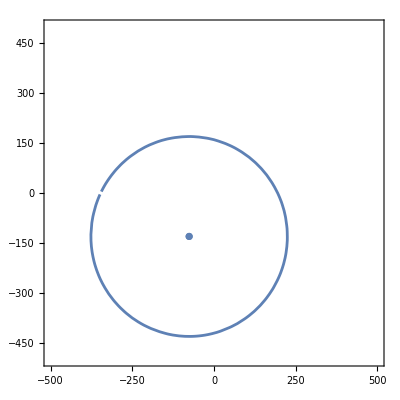

```mathematica
Show[
ContourPlot[
x^2+y^2-2 √(x^2+y^2)pmid1[[1]] Cos[ArcTan[x,y]-pmid1[[2]]]+pmid1[[1]]^2-4rad1^2==0,{x,-500,500},{y,-500,500}],
ListPolarPlot[{Reverse@pmid1}]]
```

```mathematica
With[{s=(90 π)/17},
mid1=Toxy[s]-2r1[s] Sign[{1,k[s]}~Dot~Toxy[s]] Normalize[{1,k[s]}];
mid2=-(Toxy[s]+-Sign[{1,k[s]}~Dot~Toxy[s]]re[s]/Abs@Cos[dth[s]]/3 Normalize[{1,k[s]}]);
rad1=r1[s];]
```

```mathematica
N[rad1,10]
```

150.2708834

```mathematica
pmid1//N[#,10]&
```

{151.081,-2.09792}

```mathematica
pmid1=CoordinateTransform["Cartesian"->"Polar",mid2//N[#,10]&]
```

{300.1355334,0.9540513881}

```mathematica
CoordinateTransform["Cartesian"->"Polar",-Toxy[(90 π)/17]]//N[#,10]&
```

{450.,0.9239978393}

```mathematica
CoordinateTransform["Cartesian"->"Polar",Toxy[(90 π)/17]]//N[#,10]&
```

{450.,-2.217594814}

```mathematica
%1146[[2]]-%1147[[2]]
```

3.141592654

```mathematica
rad1
```

150 Csc[(7 π)/34-ArcTan[(450 Cos[(7 π)/34]-(85 Sin[(7 π)/34])/π)/(-(85 Cos[(7 π)/34])/π-450 Sin[(7 π)/34])]]

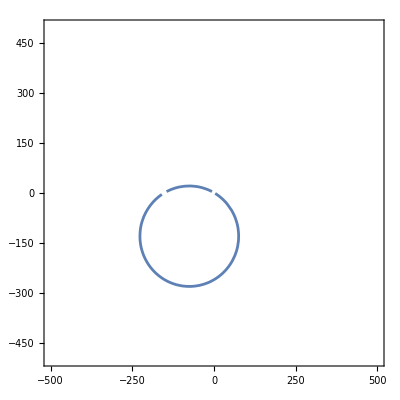

```mathematica
ContourPlot[x^2+y^2-2 √(x^2+y^2)2rad1 Cos[ArcTan[x,y]-pmid1[[2]]]-pmid1[[1]]^2+4rad1^2==0,{x,-500,500},{y,-500,500}]
```

```mathematica
-2.21759481429867758009127768231494321238`10.+2Pi
```

4.065590493